# Reprodução exemplo monografia Pedro Loques

```mathematica
Clear["Global`*"]
```

```mathematica
<<"C:\\Users\\pedro\\Documents\\Estudos\\UFRJ\\campos e ondas\\aplicacaoCamposOndas\\EletrodosFinitos.m"
```

## Parâmetros

```mathematica
freq=10^-15;
ω=2 Pi freq;
μ0=4 10^-7 Pi;
ϵ0=8.8549 10^-12;
```

### Solo

```mathematica
σ0=0.001;
Δi=11.7 10^-3;
α=0.70;
μrsolo=1.0;
sjweSolo=σ0+Δi (ω/(2 10^6 Pi)) (I + 1/Tan[Pi/2 + α]);
sjweAr=I ω ϵ0;
coefReflexao=(sjweSolo - sjweAr)/(sjweSolo + sjweAr);
γ=Sqrt[I ω μ0 sjweSolo];
```

### Condutor

```mathematica
σ=10^8;
ϵr=1.0;
μrcondutor=1.0;
R=0.01;
h=0.5;
zinterno=1/(2 Pi R) Sqrt[I μ0 ω/σ];
```

#### Eletrodos

```mathematica
nodes={
{-1.,0.,-0.5},
{1.,0.,-0.5},
{0.,1.,-0.5},
{0.,0.,-0.5},
{0.,-1.,-0.5}
};
```

```mathematica
eletrodos={
{nodes[[1]],nodes[[4]],R,zinterno},
{nodes[[2]],nodes[[4]],R,zinterno},
{nodes[[4]],nodes[[3]],R,zinterno},
{nodes[[4]],nodes[[5]],R,zinterno}
};
```

```mathematica
correntesInjetadas=Table[0,nodes//Length];
correntesInjetadas[[4]]=1.0;
```

#### Imagens

```mathematica
nodesImagens={
{-1.,0.,0.5},
{1.,0.,0.5},
{0.,1.,0.5},
{0.,0.,0.5},
{0.,-1.,0.5}
};
```

```mathematica
imagens={
{nodesImagens[[1]],nodesImagens[[4]],R,zinterno},
{nodesImagens[[2]],nodesImagens[[4]],R,zinterno},
{nodesImagens[[4]],nodesImagens[[3]],R,zinterno},
{nodesImagens[[4]],nodesImagens[[5]],R,zinterno}
};
```

## Cálculos

```mathematica
{zt, zl} = ImpedanciaEletrodos[eletrodos,γ,sjweSolo,μ0,ω,False];
{zt, zl} = IncluirImagensImpedancia[zt,zl,eletrodos,imagens,γ,sjweSolo,μ0,ω,1.0,False];
```

```mathematica
{u, it, il} = ResolverEletrodos[eletrodos,zt,zl,correntesInjetadas,nodes];
```

Pontos nos quais calcular o potencial

```mathematica
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
p=Range[-1.,1,.1];
{xx,yy}=meshgrid[p,p];
pontos2d=Flatten[{xx,yy},{2,3}];
```

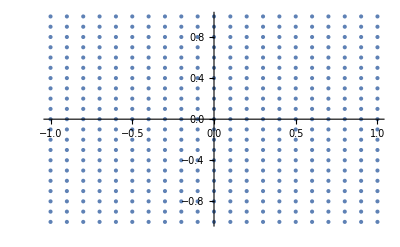

```mathematica
ListPlot[pontos2d]
```

```mathematica
pot=ParallelTable[
Abs[CalcularPotencial[Join[p,{0}],eletrodos,it,γ,sjweSolo,1]+CalcularPotencial[Join[p,{0}],imagens,it,γ,sjweSolo,1]]
,{p,pontos2d}
];//AbsoluteTiming
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{0.370079,Null}

```mathematica
pot//Max
pot//Min
Max[pot]-Min[pot]
```

229.762

107.033

122.729

```mathematica
pts=Table[{pontos2d[[i,1]],pontos2d[[i,2]],pot[[i]]},{i,pontos2d//Length}];
```

```mathematica
ListPlot3D[pts,PlotRange->All,Mesh->35,ColorFunction->"Rainbow",Axes->False,PlotLegends->Automatic,Boxed->True]
```

-Graphics3D-

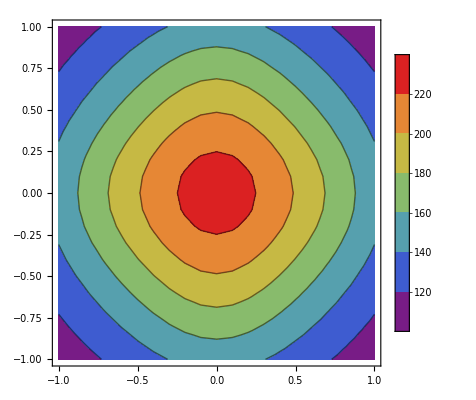

```mathematica
ListContourPlot[pts,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
Grid[Join[{{"Node","Potencial (V)"}},Transpose[{nodes,u}]],Frame->All]
```

Node | Potencial (V)
{-1.,0.,-0.5} | 333.555-6.2539×10^-15 ⅈ
{1.,0.,-0.5} | 333.555-6.2539×10^-15 ⅈ
{0.,1.,-0.5} | 333.555-6.2539×10^-15 ⅈ
{0.,0.,-0.5} | 333.555+6.2461×10^-15 ⅈ
{0.,-1.,-0.5} | 333.555-6.2539×10^-15 ⅈ

```mathematica
Grid[Join[{{"Corrente Transversal (A)","Corrente Longitudinal (A)"}},Transpose[{it,il}]],Frame->All]
```

Corrente Transversal (A) | Corrente Longitudinal (A)
0.25-3.40784×10^-33 ⅈ | -0.125+6.51338×10^-33 ⅈ
0.25-2.65029×10^-33 ⅈ | -0.125+2.14153×10^-33 ⅈ
0.25+6.89912×10^-33 ⅈ | 0.125+3.44956×10^-33 ⅈ
0.25+6.5873×10^-33 ⅈ | 0.125+3.29365×10^-33 ⅈ

Todos os resultados concordam.